## Spline with discontinuous 2nd deriv

```mathematica
q=Function[x,a x^3+b x^2+c x+d];
sol=Solve[{q[x1]==y1,q[x2]==y2,q'[x1]==0,q'[x2]==0},{a,b,c,d}][[1]]
```

{a→-(2 (y1-y2))/(x1-x2)^3,b→(3 (x1+x2) (y1-y2))/(x1-x2)^3,c→-(6 x1 x2 (y1-y2))/(x1-x2)^3,d→y1+((-x1^3+3 x1^2 x2) (y1-y2))/(x1-x2)^3}

```mathematica
q/.sol
```

```mathematica
qq=Function[{x,x1,x2,y1,y2},-((2 (y1-y2)) x^3)/(x1-x2)^3+((3 (x1+x2) (y1-y2)) x^2)/(x1-x2)^3-((6 x1 x2 (y1-y2)) x)/(x1-x2)^3+(y1+((-x1^3+3 x1^2 x2) (y1-y2))/(x1-x2)^3)]
```

Function[{x,x1,x2,y1,y2},-((2 (y1-y2)) x^3)/(x1-x2)^3+((3 (x1+x2) (y1-y2)) x^2)/(x1-x2)^3-((6 x1 x2 (y1-y2)) x)/(x1-x2)^3+(y1+((-x1^3+3 x1^2 x2) (y1-y2))/(x1-x2)^3)]

```mathematica
qq[x,1,4,3,6]
```

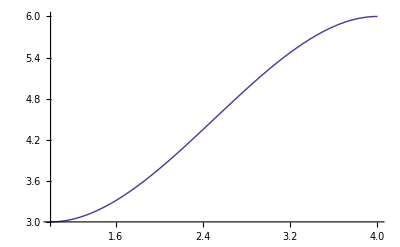

```mathematica
Plot[qq[x,1,4,3,6],{x,1,4}]
```

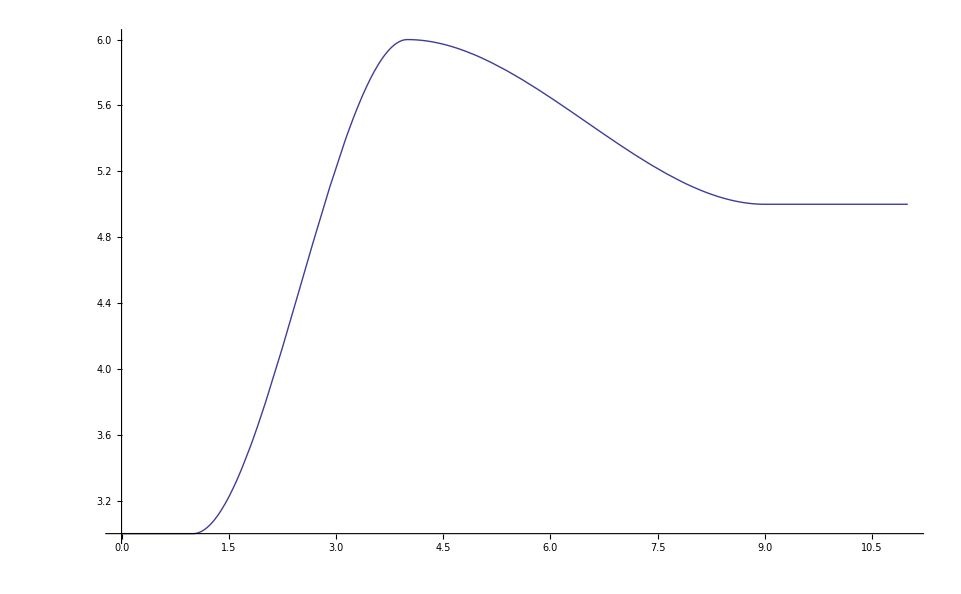

```mathematica
q1=Function[x,qq[x,1,4,3,6]];
q2=Function[x,qq[x,4,9,6,5]];
b=Function[x,Which[
x<1,q1[1],
1≤x<4,q1[x],
4≤x<9,q2[x],
9<x,q2[9]
]];
Plot[b[x],{x,0,11}]
```

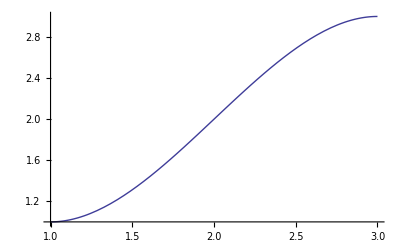

```mathematica
Block[{x1=1,x2=3,y1=1,y2=3},
Plot[q[x]/.sol,{x,x1,x2}]
]
```

## Cubic spline

```mathematica
Exit[]
```

```mathematica
q1=Function[x,a1 x^3+b1 x^2+c1 x+d1];
q2=Function[x,a2 x^3+b2 x^2+c2 x+d2];
eq={
q1[s1]==r1,q2[s3]==r3,
q1'[s1]==0,q2'[s3]==0,
q1[s2]==r2,q2[s2]==r2,
q1'[s2]==q2'[s2],
q1''[s2]==q2''[s2]
};
sol=Solve[eq,{a1,b1,c1,d1,a2,b2,c2,d2}][[1]];
p3bell=Function[s,Which[
s<s1,q1[s1],
s1≤s<s2,q1[s],
s2≤s<s3,q2[s],
s3≤s,q2[s3]
]/.sol]
```

Function[s,Which[s<s1,q1[s1],s1≤s<s2,q1[s],s2≤s<s3,q2[s],s3≤s,q2[s3]]/.sol]

```mathematica
p3pts={{1,3},{2.8,8},{3,5}};
LocatorPane[Dynamic[p3pts],
Dynamic[
{{s1,r1},{s2,r2},{s3,r3}}=p3pts;
Plot[p3bell[x],{x,0.8s1,1.2s3},PlotStyle->{Green,Thickness[0.01]},AxesLabel->{"Smem","p3[Smem]"},PlotRange->{{0.8s1,1.2 s3},{0,r2 1.5}},ImageSize->Full]
]]
```

```mathematica
p3bell=With[{
q1=Function[x,a1 x^3+b1 x^2+c1 x+d1],
q2=Function[x,a2 x^3+b2 x^2+c2 x+d2]},
With[{eq={
q1[s1]==r1,q2[s3]==r3,
q1'[s1]==0,q2'[s3]==0,
q1[s2]==r2,q2[s2]==r2,
q1'[s2]==q2'[s2],
q1''[s2]==q2''[s2]
}},
With[{sol=Solve[eq,{a1,b1,c1,d1,a2,b2,c2,d2}][[1]]},
Function[s,Which[
s<s1,q1[s1],
s1≤s<s2,q1[s],
s2≤s<s3,q2[s],
s3≤s,q2[s3]waza
]/.sol/.pθ0]
]
]
];
```

```mathematica
p3pts={{1,3},{2,8},{4,1}};
Off[InterpolatingFunction::dmval]
LocatorPane[Dynamic[p3pts],
Dynamic[
f=Interpolation[p3pts/.{x_,a___,y_}:>{x-{1,0},x,a,y,y+{1,0}}/.{}/.{x_,y_}->{{x},y,0},Method->"Spline"];
Plot[f[x],{x,-1,5},PlotRange->{-1,10}]
]]
```

```mathematica
Array[{#,2}&,8,0]
```

{{0,2},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2}}

```mathematica
p3pts=Array[{#,2}&,9,0];
Off[InterpolatingFunction::dmval]
LocatorPane[Dynamic[p3pts],
Dynamic[
p3pts[[1,1]]=0;
p3pts[[-1,1]]=8;
f=Interpolation[Sort[p3pts]/.{x_,y_}->{{x},y},Method->"Spline"];
Plot[Clip[f[x],{0,1000}],{x,-1,p3pts[[-1,1]]},PlotRange->{-1,10}]
]]
```

```mathematica
p3pts/.{x_,a___,y_}:>{x-{20,0},x-{10,0},x,a,y,y+{1,0},y+{2,0}}
```

{{-19.265,3.2},{-9.265,3.2},{0.735,3.2},{1.17,9.7},{4.,1.},{5.,1.},{6.,1.}}

```mathematica
p3pts/.{x_,y_}->{{x},y}/.{x_,a___,y_}:>{Append[x,0],a,Append[y,0]}
```

{{{1},3,0},{{2},8},{{4},1,0}}

## Warping

```mathematica
Method->"Spline"
```

```mathematica
p3pts={#,#}&/@Range[-3,3,1];
```

```mathematica
Off[InterpolatingFunction::dmval]
LocatorPane[Dynamic[p3pts],
Dynamic[
p3pts=Thread[{p3pts[[All,1]],Sort[p3pts[[All,2]]]}];
f=Interpolation[p3pts,InterpolationOrder->3,Method->"Spline"];
Plot[f[x],{x,-3,3},PlotRange->{-3,3}]
]]
```

```mathematica
Dynamic[Plot[{Exp[-(f[x])^2],Exp[-(x)^2]},{x,-3,3}]]
```

## Bezier

```mathematica
p3old=p3[0]/.p3sigmoid/.pθ0/.Smem[0][t]->x
```

(1.5-1.498/(1+ⅇ^(106. (-0.1+x))))/(1+ⅇ^(1.2 (-1.5+x)))

```mathematica
p3pts={#,0.0}&/@Union[Range[0,0.3,0.1],Range[-1.,3,0.1]]
```

{{-1.,0.},{-0.9,0.},{-0.8,0.},{-0.7,0.},{-0.6,0.},{-0.5,0.},{-0.4,0.},{-0.3,0.},{-0.2,0.},{-0.1,0.},{0.,0.},{0.1,0.},{0.1,0.},{0.2,0.},{0.2,0.},{0.3,0.},{0.3,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.8,0.},{0.9,0.},{1.,0.},{1.1,0.},{1.2,0.},{1.3,0.},{1.4,0.},{1.5,0.},{1.6,0.},{1.7,0.},{1.8,0.},{1.9,0.},{2.,0.},{2.1,0.},{2.2,0.},{2.3,0.},{2.4,0.},{2.5,0.},{2.6,0.},{2.7,0.},{2.8,0.},{2.9,0.},{3.,0.}}

```mathematica
Off[InterpolatingFunction::dmval]
LocatorPane[Dynamic[p3pts],
Dynamic[
f=BezierFunction[p3pts];
h=Interpolation[f/@Range[0.,1.,0.01],Method->"Spline"];
g=ParametricPlot[f[x],{x,0,1},PlotRange->{{-1,4},{-1,3}}];
Show[g,Plot[{p3old,h[x]},{x,0,3}],PlotLabel->Mean@Abs[(h[x]-p3old)/.x->Range[-1,3.0,0.01]],ImageSize->Full]
]]
```

```mathematica
A=Symbol["a"<>ToString[#]]&/@Range[Length[Flatten[p3pts]]];
sol=FindMinimum[loss[A],Transpose[{A,Flatten[p3pts]}],EvaluationMonitor:>(p3pts=Partition[A,2])]
p3pts=Partition[A/.sol[[2]],2];
```

FindMinimum::nrnum: The function value loss[{-1., 0., -0.9, 0., -0.8, 0., -0.7, 0., -0.6, 0., -0.5, 0., -0.4, 0., -0.3, 0., -0.2, 0., -0.1, 0., 0., 0., 0.1, 0., 0.1, 0., 0.2, 0., 0.2, 0., 0.3, 0., 0.3, 0., 0.4, 0., 0.5, 0., 0.6, 0., 0.7, 0., 0.8, 0., 0.9, 0., 1., 0., 1.1, 0., « 38 »}] is not a real number at {a1, a2, a3, a4, a5, a6, a7, a8, a9, a10, a11, a12, a13, a14, a15, a16, a17, a18, a19, a20, a21, a22, a23, a24, a25, a26, a27, a28, a29, a30, a31, a32, a33, a34, a35, a36, a37, a38, a39, a40, a41, a42, a43, a44, a45, a46, a47, a48, a49, a50, « 38 »} = {-1., 0., -0.9, 0., -0.8, 0., -0.7, 0., -0.6, 0., -0.5, 0., -0.4, 0., -0.3, 0., -0.2, 0., -0.1, 0., 0., 0., 0.1, 0., 0.1, 0., 0.2, 0., 0.2, 0., 0.3, 0., 0.3, 0., 0.4, 0., 0.5, 0., 0.6, 0., 0.7, 0., 0.8, 0., 0.9, 0., 1., 0., 1.1, 0., « 38 »}.

FindMinimum[loss[A],Transpose[{A,Flatten[p3pts]}],EvaluationMonitor:>(p3pts=Partition[A,2])]

ReplaceAll::reps: {a1, -1.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {a2, 0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {a3, -0.9} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
loss[A_?(VectorQ[#,NumericQ]&)]:=Module[{},
f=BezierFunction[Partition[A,2]];
h=Interpolation[f/@Range[0.,1.,0.1],Method->"Spline"];
Mean@Abs[(h[x]-p3old)/.x->Range[-1,3.0,0.01]]
]
```

## Sigmoid product

```mathematica
Manipulate[
Plot[{((p3b-p3d)/(1+Exp[(s-p3a) p3c])+p3d),
(1/(1+Exp[(s-p3e) p3f])),
((p3b-p3d)/(1+Exp[(s-p3a) p3c])+p3d) (1/(1+Exp[(s-p3e) p3f]))},{s,0,8},PlotRange->{0,2},ImageSize->Full],
{{p3a,2},0,8},{{p3b,0},0,1},{{p3c,10},0,10},{{p3d,2},0,2},{{p3e,6},0,8},{{p3f,5},0,10}]
```

## linear part

```mathematica
{v,θ0}={{p4b, p2, p3a, p3b, p3c, p3d, p3e, p3f, p5, StotNative, StotOpt, StotOE, maxdose, dX}, {8., 1., 0.1, 0.002, 106., 1.5, 1.5, 1.2, 5., 1.2, 3., 80., 0.01, 0.0001}};
```

```mathematica
p3sigmoid=Function[s,p3[s]->((p3b-p3d)/(1+Exp[(Smem[s][t]-p3a)p3c])+p3d)(1/(1+Exp[(Smem[s][t]-p3e)p3f]))]/@{0,1}
```

```mathematica
p3old=((p3b-p3d)/(1+Exp[(Smem[s][t]-p3a)p3c])+p3d)(1/(1+Exp[(Smem[s][t]-p3e)p3f]))/.pθ0/.Smem[s][t]->s
```

```mathematica
p3old=(1.5-1.498/(1+ⅇ^(106. (-0.1+s))))/(1+ⅇ^(1.2 (-1.5+s)));
```

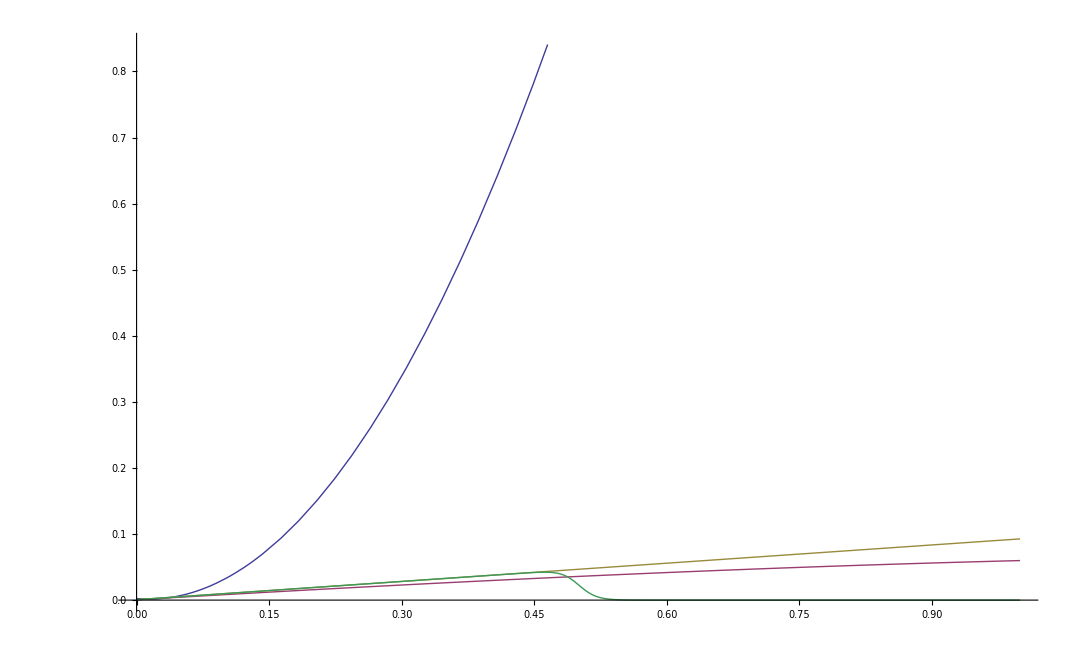

```mathematica
p3new=(p3m*s+p3n)(1/(1+Exp[(Smem[s][t]-p3e)p3f]))/.{p3e->0.5,p3f->100}/.pθ0/.Smem[s][t]->s;
Plot[{lineq,p3old,p3[0]/.p3sigmoid/.Smem[0][t]->s/.pθ0,p3new},{s,0,1}]
```

```mathematica
lineq=Fit[{s,p3old}/.s->Range[0,0.05,0.001]//Transpose,{1,s,s^2},s]
```

0.00231613-0.113518 s+4.11554 s^2

```mathematica
p3new=(p3m*s+p3n)(1/(1+Exp[(Smem[s][t]-p3e)p3f]))/.{p3e->0.2,p3f->10}/.pθ0/.Smem[s][t]->s;
```

```mathematica
θ0={8.,1.,0.1,0.002,106.,1.5,2.,5,0.092,0.00064,5.,1.2,3.,80.,0.01,0.0001};
```